Recurrence equations (§6):

```mathematica
Quit[]
```

```mathematica
sq=Table[k^2,{k,1,10}]
sq[[9]]
```

{1,4,9,16,25,36,49,64,81,100}

81

```mathematica
cub={};
Do[AppendTo[cub,k^3],{k,1,4}]
cub[[3]]
```

27

```mathematica
cub={};
Do[AppendTo[cub,k^3];Print[cub[[k]]],{k,1,4}]
cub[[3]]
```

1

8

27

64

27

```mathematica
Do[Print[k^2],{k,1,10,3}]
```

1

16

49

100

```mathematica
Quit[]
```

```mathematica
sq={};
cub={};
Do[AppendTo [sq,k^2];AppendTo[cub,k^3],{k,-5,10}]
sq
cub
sq[[4]]
cub[[4]]
sq[[-4]]
cub[[-4]]
```

{25,16,9,4,1,0,1,4,9,16,25,36,49,64,81,100}

{-125,-64,-27,-8,-1,0,1,8,27,64,125,216,343,512,729,1000}

4

-8

49

343

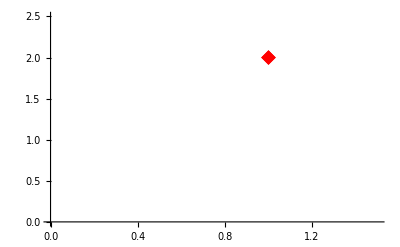

```mathematica
ListPlot[{{1,2}},PlotRange->{{0,1.5},{0,2.5}},PlotMarkers->{"◆",15},PlotStyle->Red]
```

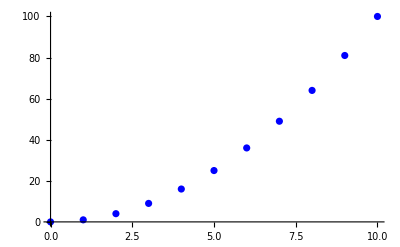

```mathematica
ListPlot[Table[{k,k^2},{k,0,10}],PlotStyle->Blue]
```

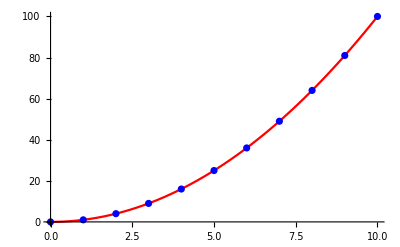

```mathematica
plotdisc=ListPlot[Table[{k,k^2},{k,0,10}],PlotStyle->Blue];
plotcont=Plot[x^2,{x,0,10},PlotStyle->Red];
Show[plotcont,plotdisc]
```

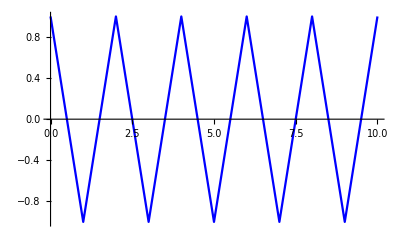

```mathematica
ListLinePlot[Table[{k,(-1)^k},{k,0,10}],PlotStyle->Blue]
```

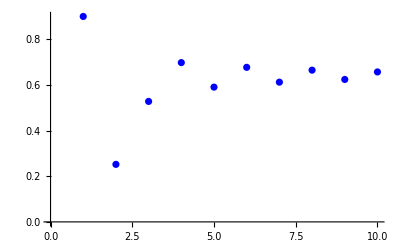

```mathematica
z=Table[0,10];
z[[1]]=0.9;
Do[z[[t+1]]=2.8*z[[t]]*(1-z[[t]]),{t,1,9}]
ListPlot[Table[{t,z[[t]]},{t,0,10}],PlotStyle->Blue]
```

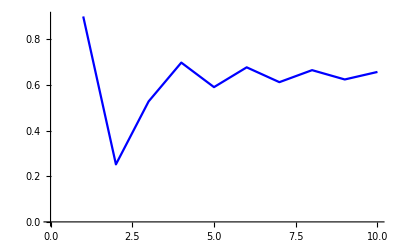

```mathematica
ListLinePlot[Table[{t,z[[t]]},{t,0,10}],PlotStyle->Black]
```

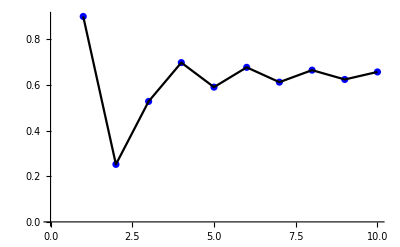

```mathematica
Show[ListPlot[Table[{t,z[[t]]},{t,0,10}],PlotStyle->Blue],ListLinePlot[Table[{t,z[[t]]},{t,0,10}],PlotStyle->Black]]
```

```mathematica
Quit[]
```

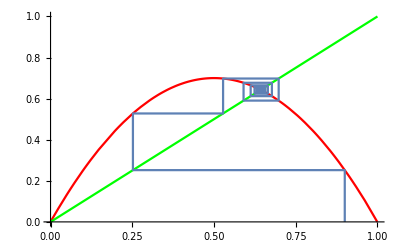

```mathematica
F[z_]:=2.8*z*(1-z)
pF=Plot[F[z],{z,0,10},PlotRange->{{0,1},{0,1}},PlotStyle->Red];
diag=Plot[z,{z,0,10},PlotRange->{{0,1},{0,1}},PlotStyle->Green];
n=20;
z=Table[0,n+1];
z[[1]]=0.9;
Do[z[[t+1]]=2.8*z[[t]]*(1-z[[t]]),{t,1,n}]
x=Table[z[[1]],2*n];
y=Table[0,2*n];
y[[2]]=z[[2]];
Do[x[[2*t]]=z[[t]];x[[2*t-1]]=z[[t]];y[[2*t]]=z[[t+1]];y[[2*t-1]]=z[[t]],{t,2,n}]
coblines=ListLinePlot[Table[{x[[t]],y[[t]]},{t,1,2*n-1}]];
Show[pF,diag,coblines]
```